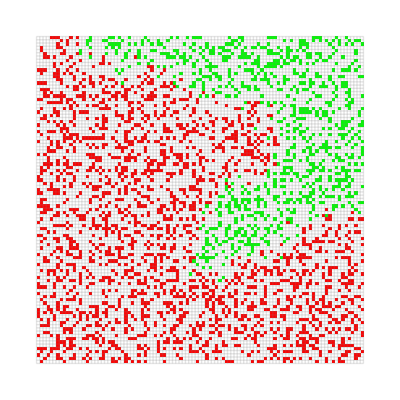

```mathematica
ClearAll["summative`*"];
SetDirectory[NotebookDirectory[]];
<< "SummativeLibrary.wl";

(* States *)
EMPTY=0;
SPECIES1=1;
SPECIES2=2;
COMP21=1;

r=50;c=r+1;w=2r+1;
m = ConstantArray[EMPTY,{w,w}];
m[[1,1]]=SPECIES1;
m[[w,w]]=SPECIES2;
Do[(
x=RandomInteger[{1,w}];
y=RandomInteger[{1,w}];
m[[x,y]]=RandomInteger[{1,2}];
),20];
fertileness=RandomReal[1,{w,w}];

mNextState=Function[{matrix},
effect=ListConvolve[mEffectMatrix[4],matrix,5];
effect1=ListConvolve[mEffectMatrix[4],matrix,5,0,
(#1*Boole[#2==SPECIES1])&,Plus];
effect2=ListConvolve[mEffectMatrix[4],matrix,5,0,
(#1*Boole[#2==SPECIES2])&,Plus];
x++;
MapThread[mNextCell,{matrix,effect1,effect2,fertileness},2]
];

mNextCell=Function[{cell,e1,e2,fertileness},
Switch[cell,
2,0,
1,0,
0,compete[e1,e2,fertileness]
]
];

compete[ev1_,ev2_,f_]:=
If[RandomReal[ev1+COMP21*ev2]<ev1,
1*Boole[RandomReal[]≤f*mProbSeeding[0.3,ev1]],
2*Boole[RandomReal[]≤f*mProbSeeding[0.3,ev2]]];

gens=30;
x=0;ProgressIndicator[Dynamic[x/gens]]
results=NestList[mNextState,m,gens];
colors={EMPTY->White,SPECIES1->Red,SPECIES2->Green};
ListAnimate[Map[ArrayPlot[#,ColorRules->colors,Mesh->True,MeshStyle->RGBColor[0.5,0.5,0.5,0.2]]&,results],AnimationRunning->False,Frame->False]
ArrayPlot[results//Last,ColorRules->colors,Mesh->True,MeshStyle->RGBColor[0.5,0.5,0.5,0.2]]
```